```mathematica
Clear[X]
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"Month","Day"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\2\cylinder\0.7-0.4C

09_10

-Graphics3D-

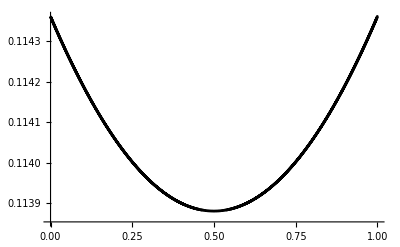

```mathematica
X[u_,v_]:={Sin[v],Cos[v],u};
X2[u_,v_]:={v,v,1};
uu=Import["uu_2_26_"<>date<>".txt","Table"];
vv=Import["vv_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Flatten[vv];

str=Import["str_.txt","Table"]//Flatten;


points=MapThread[X,{uu,vv}];
str=Import["str_.txt","Table"]; 
str = Flatten[str];
strMin=Min[str];
strMax=Max[str];

strN=Rescale[str,{strMin,strMax}];

points=MapThread[X,{uu,vv}];
color = ColorData["TemperatureMap"]/@strN;
V2k=Graphics3D[{Thickness[0.02],Line[points,VertexColors->color]}];
V3k=Graphics3D[{Thickness[0.02],Yellow,Line[points]}];

V3=ParametricPlot3D[X[u,v],{u,0,Pi},{v,0,2Pi},PlotStyle->Directive[LightRed]];

Legended[Show[V3,V2k,PlotRange->All,Boxed->False,Axes->False],BarLegend[{"TemperatureMap",{strMin,strMax}},LegendLabel->"Stress"]]

Show[V3k, Background->Black];
l1x=Import["l1_2_26_"<>date<>".txt","Table"];
a6=ListLinePlot[Transpose[l1x],DataRange->{0,1},PlotStyle->{Black}]
```

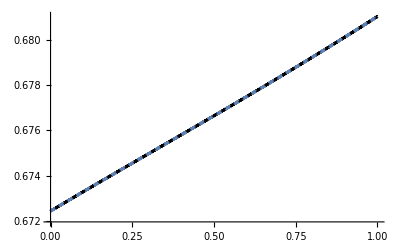

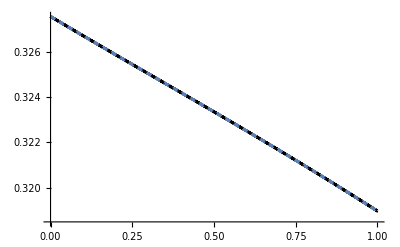

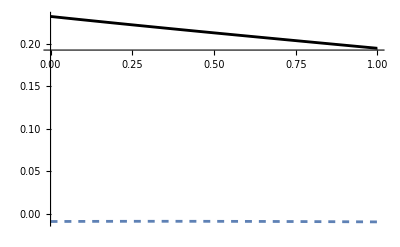

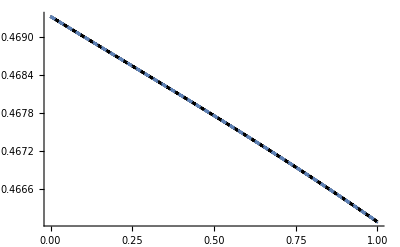

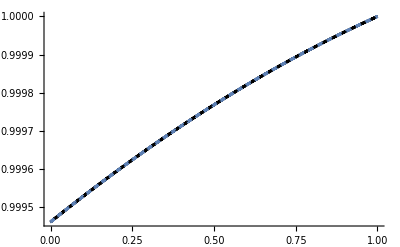

```mathematica
kn1x=Import["kn1_2_26_"<>date<>".txt","Table"];
kn2x=Import["kn2_2_26_"<>date<>".txt","Table"];
kn1xs=Import["kn1s_.txt","Table"];
kn2xs=Import["kn2s_.txt","Table"] ;

taugx=Import["taug_2_26_"<>date<>".txt","Table"];
gx=Import["g_2_26_"<>date<>".txt","Table"];
taugxs=Import["taugs_.txt","Table"] ;
gxs=Import["gs_.txt","Table"];

kgx=Import["kg_2_26_"<>date<>".txt","Table"];
kgxs=Import["kgs_.txt","Table"] ;


a1=ListLinePlot[Transpose[kn1x],DataRange->{0,1},PlotStyle->{Black}];
a1s=ListLinePlot[Transpose[kn1xs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a1,a1s]

a2=ListLinePlot[Transpose[kn2x],DataRange->{0,1},PlotStyle->{Black}];
a2s=ListLinePlot[Transpose[kn2xs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a2,a2s]

a3=ListLinePlot[Transpose[kgx],DataRange->{0,1},PlotStyle->{Black}];
a3s=ListLinePlot[Transpose[kgxs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a3,a3s, PlotRange->All]

a4=ListLinePlot[Transpose[taugx],DataRange->{0,1},PlotStyle->{Black}];
a4s=ListLinePlot[Transpose[taugxs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a4,a4s, PlotRange ->All]

a5=ListLinePlot[Transpose[gx],DataRange->{0,1},PlotStyle->{Black}];
a5s=ListLinePlot[Transpose[gxs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a5,a5s, PlotRange ->All]
```

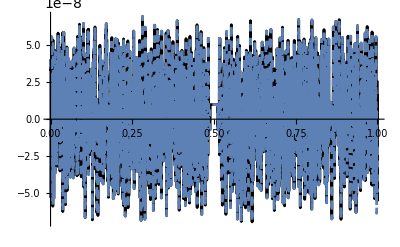

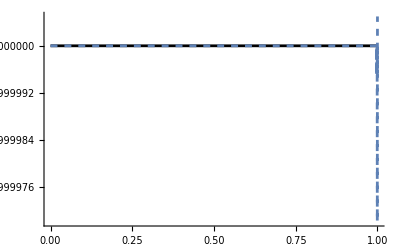

```mathematica
aG=ListLinePlot[Transpose[kn1x*kn2x - taugx*taugx],DataRange->{0,1},PlotStyle->Black];
aH=ListLinePlot[0.5*Transpose[kn1x+kn2x],DataRange->{0,1},PlotStyle->Black];

aGs=ListLinePlot[Transpose[kn1xs*kn2xs - taugxs*taugxs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
aHs=ListLinePlot[0.5*Transpose[kn1xs+kn2xs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];

Show[aG,aGs,PlotRange->All]
Show[aH,aHs,PlotRange->All]
```

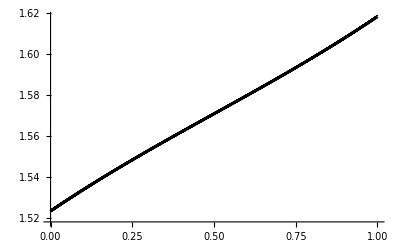

```mathematica
phix=Import["phi_2_26_"<>date<>".txt","Table"];


a1=ListLinePlot[Transpose[phix],DataRange->{0,1},PlotStyle->{Black}];
Show[a1]
```